```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/EVBK/gdc_VER_EVBK_points.txt"];
accCH=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/CH/gdc_VER_CH_points.txt"];
confVal=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_VALUE/CONF_VAL.txt"];
names=Keys[accEVBK]
confs={"DOJ","Z","F"};
timesteps=Range[17];
col2=Map[Blend[{Blue, Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]];
homeAdd="/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/";
spezAdd="CONF_VALUE/RESULTS/";
plotType="VAL";
revType="IND";

(* col1=Map[ColorData["BlueGreenYellow"][#]&,Range[Length[timesteps]]/Length[timesteps]]
col3=Map[Hue[#]&,Range[Length[timesteps]]/Length[timesteps]]
col4=Map[Hue[1,#]&,Range[Length[timesteps]]/Length[timesteps]]
col5=Map[ColorData["TemperatureMap"][#]&,Range[Length[timesteps]]/Length[timesteps]]*)
```

{DLB,MUR,LYE,PHI,SED,AUS}

```mathematica
dataTableDOJ=circTableDataFunc[confVal,"DOJ",names, revType];
dataTableZ=circTableDataFunc[confVal,"Z",names,revType];
dataTableF=circTableDataFunc[confVal,"F",names,revType];
tableDOJ=circTableFunc[dataTableDOJ,plotType];
tableZ=circTableFunc[dataTableZ,plotType];
tableF=circTableFunc[dataTableF,plotType];
```

```mathematica
(* Dec>0.01 *)
dataDOJ=sumUpFunc[accEVBK, accCH,confVal,"DOJ",names,revType];
dataZ=sumUpFunc[accEVBK, accCH,confVal,"Z",names, revType];
dataF=sumUpFunc[accEVBK, accCH,confVal,"F",names, revType];
```

```mathematica
shrinkFac1=0.01;
shrinkFac2=0.104;
plotsDOJ=Map[singlePlot[#, dataDOJ,col2,shrinkFac1,shrinkFac2,plotType]&,names];
plotsZ=Map[singlePlot[#, dataZ,col2,shrinkFac1,shrinkFac2, plotType]&,names];
plotsF=Map[singlePlot[#, dataF,col2,shrinkFac1,shrinkFac2, plotType]&,names];
```

size {0.104,0.104,0.0387644,0.0535657,0.0550216,0.0530625,0.0683047,0.070327,0.104}

size {0.0416559,0.0416559,0.0762741,0.0762741,0.0567261,0.066388,0.104,0.104}

size {0.0220329,0.0220329,0.0515298,0.0532483,0.0518506,0.0659334,0.104,0.104}

size {0.0336473,0.0511173,0.069988,0.0659334,0.0608251,0.0718112,0.104}

size {0.0511173,0.0511173,0.0490283,0.0458289,0.0474052,0.104}

size {0.0759664,0.0879056,0.104}

size {0.104,0.104,0.0363905,0.0530968,0.0543542,0.0524578,0.0679603,0.070047,0.104}

size {0.0403253,0.0404077,0.0762365,0.076238,0.0563311,0.0663653,0.104,0.104}

size {0.000138651,0.00392914,0.0510455,0.0528583,0.0515994,0.0659096,0.104,0.104}

size {0.0292977,0.0505134,0.069918,0.0658735,0.0607851,0.0717984,0.104}

size {0.050612,0.0506319,0.0486933,0.0456463,0.0472514,0.104}

size {0.0759213,0.0878939,0.104}

size {0.104,0.104,0.0997091,0.103083,0.102707,0.102825,0.103323,0.103447,0.104}

size {0.101495,0.101642,0.103925,0.103928,0.103225,0.103955,0.104,0.104}

size {0.0757505,0.0798182,0.103054,0.103235,0.103504,0.103952,0.104,0.104}

size {0.0966293,0.102826,0.10386,0.103881,0.10392,0.103974,0.104}

size {0.103014,0.103052,0.103341,0.103638,0.103695,0.104}

size {0.10391,0.103977,0.104}

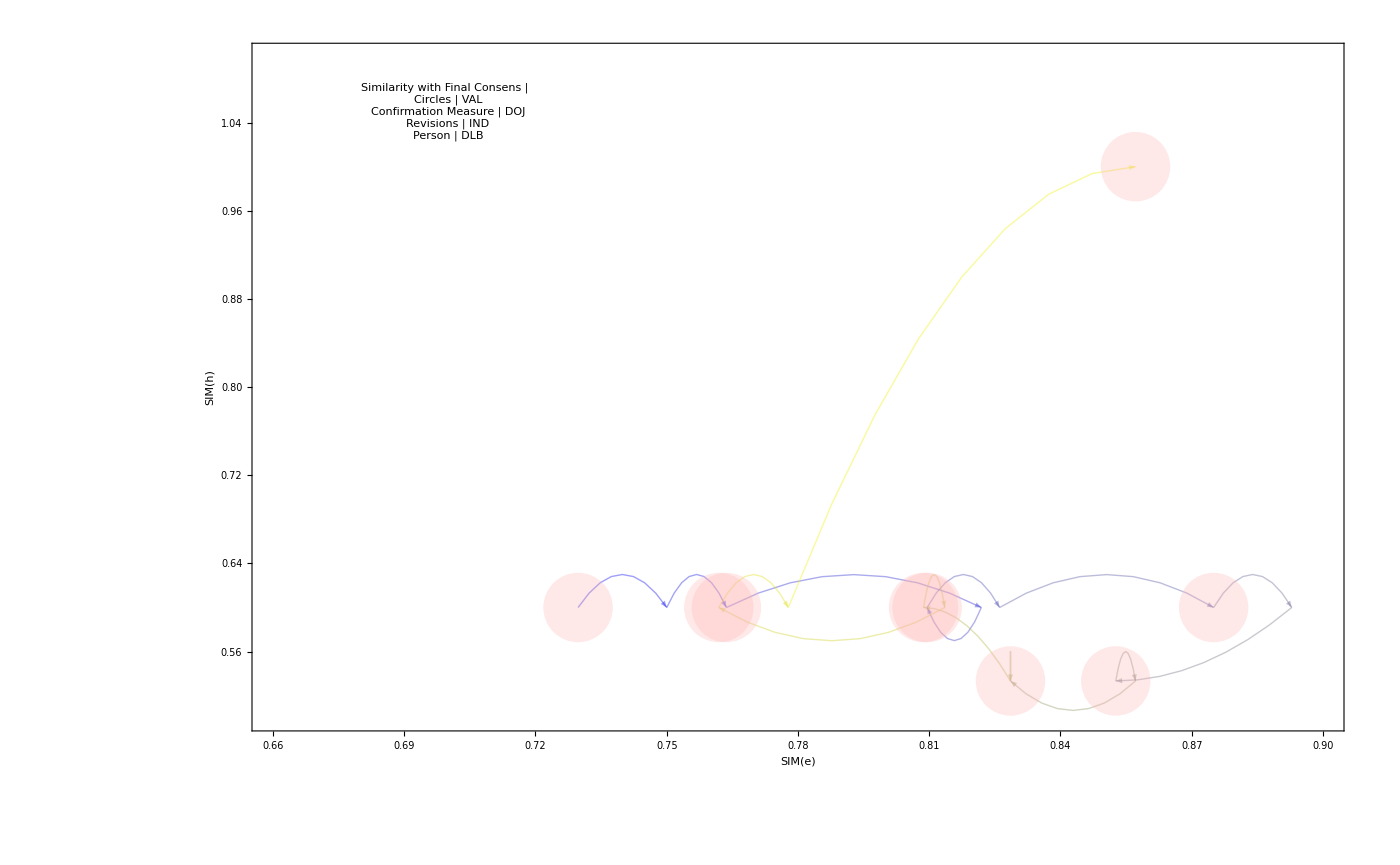

```mathematica
plotsDOJ[[1]]
```

```mathematica
SetDirectory[homeAdd<>spezAdd<>revType<>"/DOJ"];
Map[Export[ToString[plotType]<>"_DOJ_"<>ToString[names[[#]]]<>".jpeg",plotsDOJ[[#]],ImageResolution->200]&,Range[Length[names]]]
Map[Export[ToString[plotType]<>"_DOJ_"<>ToString[names[[#]]]<>"_table.jpeg",tableDOJ[[#]],ImageResolution->200]&,Range[Length[names]]]
```

{VAL_DOJ_DLB.jpeg,VAL_DOJ_MUR.jpeg,VAL_DOJ_LYE.jpeg,VAL_DOJ_PHI.jpeg,VAL_DOJ_SED.jpeg,VAL_DOJ_AUS.jpeg}

{VAL_DOJ_DLB_table.jpeg,VAL_DOJ_MUR_table.jpeg,VAL_DOJ_LYE_table.jpeg,VAL_DOJ_PHI_table.jpeg,VAL_DOJ_SED_table.jpeg,VAL_DOJ_AUS_table.jpeg}

```mathematica
SetDirectory[homeAdd<>spezAdd<>revType<>"/Z"];
Map[Export[ToString[plotType]<>"_Z_"<>ToString[names[[#]]]<>".jpeg",plotsZ[[#]],ImageResolution->200]&,Range[Length[names]]]
Map[Export[ToString[plotType]<>"_Z_"<>ToString[names[[#]]]<>"_table.jpeg",tableZ[[#]],ImageResolution->200]&,Range[Length[names]]]
```

{VAL_Z_DLB.jpeg,VAL_Z_MUR.jpeg,VAL_Z_LYE.jpeg,VAL_Z_PHI.jpeg,VAL_Z_SED.jpeg,VAL_Z_AUS.jpeg}

{VAL_Z_DLB_table.jpeg,VAL_Z_MUR_table.jpeg,VAL_Z_LYE_table.jpeg,VAL_Z_PHI_table.jpeg,VAL_Z_SED_table.jpeg,VAL_Z_AUS_table.jpeg}

```mathematica
SetDirectory[homeAdd<>spezAdd<>revType<>"/F"];
Map[Export[ToString[plotType]<>"_F_"<>ToString[names[[#]]]<>".jpeg",plotsF[[#]],ImageResolution->200]&,Range[Length[names]]]
Map[Export[ToString[plotType]<>"_F_"<>ToString[names[[#]]]<>"_table.jpeg",tableF[[#]],ImageResolution->200]&,Range[Length[names]]]
```

{VAL_F_DLB.jpeg,VAL_F_MUR.jpeg,VAL_F_LYE.jpeg,VAL_F_PHI.jpeg,VAL_F_SED.jpeg,VAL_F_AUS.jpeg}

{VAL_F_DLB_table.jpeg,VAL_F_MUR_table.jpeg,VAL_F_LYE_table.jpeg,VAL_F_PHI_table.jpeg,VAL_F_SED_table.jpeg,VAL_F_AUS_table.jpeg}